```mathematica
(*Defining variables*)
λ:=800 (*nm*)
c:=300 (*nm/fs*)
w0:= 2*π*c/λ(*rad/fs*)
I0:=1.2*10^14(*W/cm^2*)
ϵ0:=8.85*10^-12(*As/Vm*)
cm:=3*10^8(*m/s*)
e:=1.602*10^-19(*C*)
m :=9.109*10^-31(*Kg*) 
UP:=9.33*10^-14(I0)(λ*10^-3)^2 (*eV*)	
Ip:=15.7596(*eV*)
hw :=(6.582*10^-16)(w0/(1*10^-15))(*eV*)
```

```mathematica
(*The cut-off is given by: *)
1.32Ip+3.17*UP (*eV*)
```

43.5171

```mathematica
(*The best material for this cut-off is then the aluminum*)
```

```mathematica
(*The harmonic is*)
```

```mathematica
Round[(1.32Ip+3.17*UP)/hw]+1 (*To make it odd*)
```

29

```mathematica
(*Which corresponds to a radiaton of *)
29*w0//N (*PHz*)
```

68.3296

```mathematica
(*Average GDD from the classical model:*)vt[t_]:=(Sin[w0*t]-Cos[π/2(Sin[1/3(-π/2+w0*t)])])
Nh[t_]:=(Ip+2UP*vt[t]^2)/hw
```

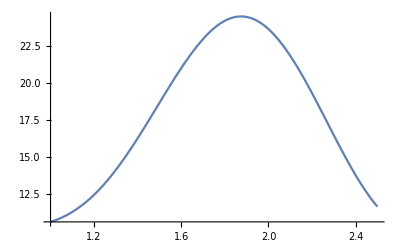

```mathematica
Plot[Nh[t],{t,1,2.5}]
```

```mathematica
(1.5-1.35)/((Nh[1.5]-Nh[1.35])*w0)(*GDD in fs^2 from the plot*)
```

0.0180404

```mathematica
(*Analysis of the image from the slide using ImageJ software. The pixels for the x and y axis were determined using the software and then the points for the slope were given by this. The values are:
(*in x*)
  47 - 87 
47- 20
87-47
40-20 
2-1 (*pixels*)
(*in y*)
0-222
0.1-187
0.0028-1 (*pixels*)*)
```

```mathematica
(*For the first point (57,180) and the second (63,202). This gives a slope of:*)
```

```mathematica
((180-202)(0.0028))/((63-57)2)//N (*(ev)*)
```

-0.00513333

```mathematica
(*In PHz*)
```

```mathematica
-0.00513/0.6582
```

-0.00779398

```mathematica
(*And the intersection is 1.10748, so the final GDD equation is: *)
(*1.10748-0.0077w0*)
```

```mathematica
(*Equation for GD*)
GD[w_,d_]:=((1.5-1.35)/((Nh[1.5]-Nh[1.35])*w0))(w-w0)+d/200(1.10748-0.00513/0.6582 w)
```

```mathematica
(*The amplitude is*)
Ampli[w_]:=Piecewise[{{1,Ip/0.6582<w<29*w0}}]
```

```mathematica
(*Since the GD is equal to dϕ/dw, we can integrate the above equation with respect to w to get the phase of the electric field and this in the form E(w) = Ampli(w)*ⅇ^(ⅈ*ϕ(w)). Now, if we calculate the absolute value and take the square value we will get the intensity. Doing this for different values of d we can estimate which thickness produce the best compression.*)
```

```mathematica
A:={}
For[i=100,i<701,i+=100,AppendTo[A,(Abs[InverseFourierTransform[Ampli[w] ⅇ^(ⅈ*∫GD[w,i]ⅆw),w,t]])^2]]
```

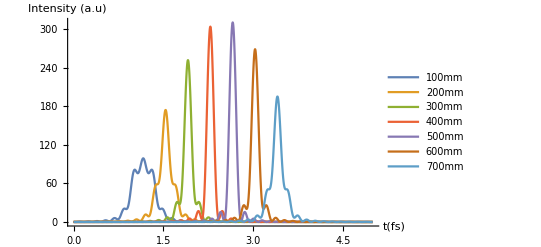

```mathematica
(*So the plot for the final pulse is*)
Plot[{A[[1]],A[[2]],A[[3]],A[[4]],A[[5]],A[[6]],A[[7]]},{t,0,5},PlotRange->All,PlotLegends->{"100mm","200mm","300mm","400mm","500mm","600mm","700mm"},AxesLabel->{"t(fs)","Intensity (a.u)"}]
```

```mathematica
(*Then the distance of the crystal should be of 500mm since it produces the highest intensity value and the most compressed pulse*)
```